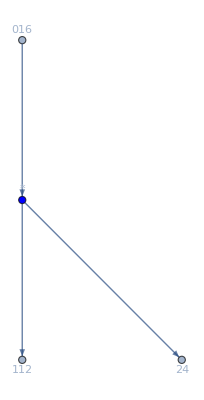

```mathematica
FullPoset[allGraphs2]
```

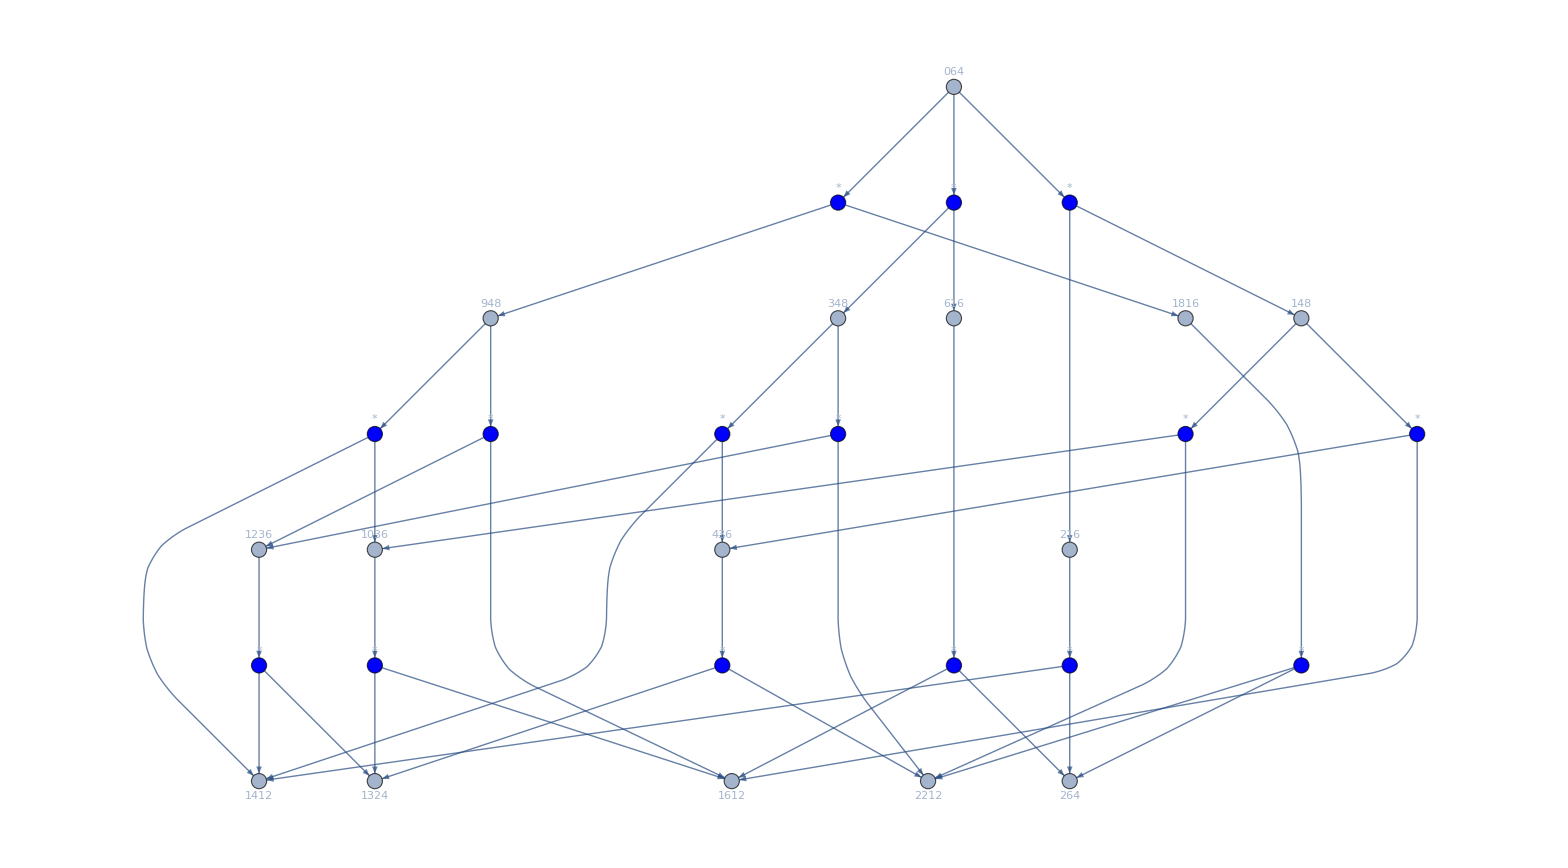

```mathematica
FullPoset[allGraphs3]
```

```mathematica
AllBut[all_,buts_]:=Select[all,!MemberQ[buts,#]&]
```

```mathematica
FullPoset2[all_]:=Block[{result={}, vertices={},edges={},  added={}},
Table[
Table[
Table[
If[all[main,"colofour"]==all[first,"colofour"]+all[second,"colofour"],
AppendTo[result,{main,{first,second}}]
]
,
{second,AllBut[Keys[all],{main, first}]}
],
{first,AllBut[Keys[all],{main}]}
]
,{main,Keys[all]}
];
vertices = Keys[all];
Table[
AppendTo[edges,res[[1]]->res[[2,1]]];
AppendTo[edges,res[[1]]->res[[2,2]]];
,{res,result}];
edges=DeleteDuplicates[edges];
added=DeleteDuplicates[added];
vertices=Join[added,vertices];
Graph[
vertices,
edges,
VertexLabels->Join[
Map[#->Labeled[Framed[ShowGraph[all,#]],Style[Factor[ChromaticPolynomial[all[#,"graph"],4]],Green]]&,Keys[all]],
Map[#->Tooltip["*",Column[#]]&,added]
],
VertexStyle->Map[#->Blue&,added],
GraphLayout->"LayeredDigraphEmbedding"
]
];
```

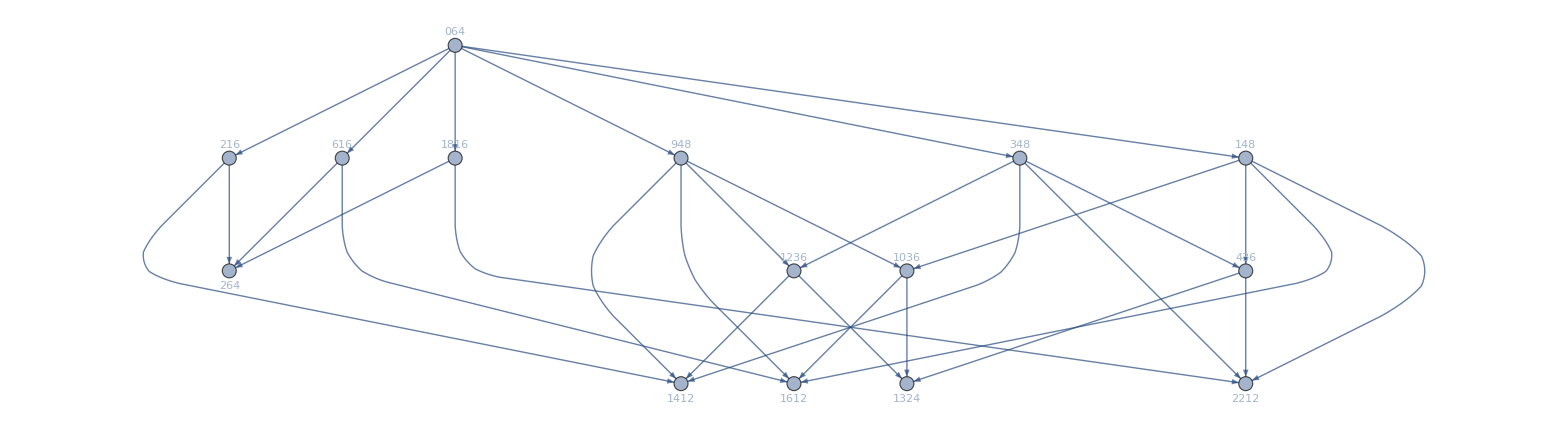

```mathematica
FullPoset2[allGraphs3]
```

```mathematica
Table[Select[Keys[allGraphs2],MemberQ[ListofVars[allGraphs2[#,"colofour"]],allGraphs2[k,"colofour"]]&],{k,allGraphs2AtomKeys}]
```

{{0,1},{0,2}}

```mathematica
Table[Select[Keys[allGraphs3],MemberQ[ListofVars[allGraphs3[#,"colofour"]],allGraphs3[k,"colofour"]]&],{k,allGraphs3AtomKeys}]
```

{{0,9,12,13,10,3,4,1},{0,9,12,14,3,2},{0,9,16,10,6,1},{0,18,22,3,4,1},{0,18,26,6,2}}

```mathematica
fourKeys=Select[Keys[allGraphs4],VertexCount[allGraphs4[#,"graph"]]==4&]
```

{0,243,324,351,360,363,364,361,354,355,352,333,336,337,334,327,328,325,270,279,282,283,280,273,274,271,252,255,256,253,246,247,244,81,108,117,120,121,118,111,112,109,90,93,94,91,84,85,82,27,36,39,40,37,30,31,28,9,12,13,10,3,4,1}

```mathematica
Table[{Length[Select[fourKeys,MemberQ[ListofVars[allGraphs4[#,"colofour"]],allGraphs4[k,"colofour"]]&]]/Length[fourKeys],k},{k,allGraphs4AtomKeys}]//Sort
```

{{1/64,728},{1/8,377},{1/8,473},{1/8,637},{1/8,697},{1/4,400},{1/4,448},{1/4,608},{1/2,365},{1/2,367},{1/2,373},{1/2,391},{1/2,445},{1/2,607},{1,364}}

```mathematica
Table[{Length[Select[Keys[allGraphs4],MemberQ[ListofVars[allGraphs4[#,"colofour"]],allGraphs4[k,"colofour"]]&]]/Length[Keys[allGraphs4]],k},{k,allGraphs4AtomKeys}]//Sort
```

{{15/127,728},{22/127,377},{22/127,473},{22/127,637},{22/127,697},{26/127,400},{26/127,448},{26/127,608},{40/127,365},{40/127,367},{40/127,373},{40/127,391},{40/127,445},{40/127,607},{64/127,364}}

```mathematica
fiveKeys=Select[Keys[allGraphs5],VertexCount[allGraphs5[#,"graph"]]==5&]
```

{0,19683,26244,28431,29160,29403,29484,29511,29520,29523,29524,29521,29514,29515,29512,29493,29496,29497,29494,29487,29488,29485,29430,29439,29442,29443,29440,29433,29434,29431,29412,29415,29416,29413,29406,29407,29404,29241,29268,29277,29280,29281,29278,29271,29272,29269,29250,29253,29254,29251,29244,29245,29242,29187,29196,29199,29200,29197,29190,29191,29188,29169,29172,29173,29170,29163,29164,29161,28674,28755,28782,28791,28794,28795,28792,28785,28786,28783,28764,28767,28768,28765,28758,28759,28756,28701,28710,28713,28714,28711,28704,28705,28702,28683,28686,28687,28684,28677,28678,28675,28512,28539,28548,28551,28552,28549,28542,28543,28540,28521,28524,28525,28522,28515,28516,28513,28458,28467,28470,28471,28468,28461,28462,28459,28440,28443,28444,28441,28434,28435,28432,26973,27216,27297,27324,27333,27336,27337,27334,27327,27328,27325,27306,27309,27310,27307,27300,27301,27298,27243,27252,27255,27256,27253,27246,27247,27244,27225,27228,27229,27226,27219,27220,27217,27054,27081,27090,27093,27094,27091,27084,27085,27082,27063,27066,27067,27064,27057,27058,27055,27000,27009,27012,27013,27010,27003,27004,27001,26982,26985,26986,26983,26976,26977,26974,26487,26568,26595,26604,26607,26608,26605,26598,26599,26596,26577,26580,26581,26578,26571,26572,26569,26514,26523,26526,26527,26524,26517,26518,26515,26496,26499,26500,26497,26490,26491,26488,26325,26352,26361,26364,26365,26362,26355,26356,26353,26334,26337,26338,26335,26328,26329,26326,26271,26280,26283,26284,26281,26274,26275,26272,26253,26256,26257,26254,26247,26248,26245,21870,22599,22842,22923,22950,22959,22962,22963,22960,22953,22954,22951,22932,22935,22936,22933,22926,22927,22924,22869,22878,22881,22882,22879,22872,22873,22870,22851,22854,22855,22852,22845,22846,22843,22680,22707,22716,22719,22720,22717,22710,22711,22708,22689,22692,22693,22690,22683,22684,22681,22626,22635,22638,22639,22636,22629,22630,22627,22608,22611,22612,22609,22602,22603,22600,22113,22194,22221,22230,22233,22234,22231,22224,22225,22222,22203,22206,22207,22204,22197,22198,22195,22140,22149,22152,22153,22150,22143,22144,22141,22122,22125,22126,22123,22116,22117,22114,21951,21978,21987,21990,21991,21988,21981,21982,21979,21960,21963,21964,21961,21954,21955,21952,21897,21906,21909,21910,21907,21900,21901,21898,21879,21882,21883,21880,21873,21874,21871,20412,20655,20736,20763,20772,20775,20776,20773,20766,20767,20764,20745,20748,20749,20746,20739,20740,20737,20682,20691,20694,20695,20692,20685,20686,20683,20664,20667,20668,20665,20658,20659,20656,20493,20520,20529,20532,20533,20530,20523,20524,20521,20502,20505,20506,20503,20496,20497,20494,20439,20448,20451,20452,20449,20442,20443,20440,20421,20424,20425,20422,20415,20416,20413,19926,20007,20034,20043,20046,20047,20044,20037,20038,20035,20016,20019,20020,20017,20010,20011,20008,19953,19962,19965,19966,19963,19956,19957,19954,19935,19938,19939,19936,19929,19930,19927,19764,19791,19800,19803,19804,19801,19794,19795,19792,19773,19776,19777,19774,19767,19768,19765,19710,19719,19722,19723,19720,19713,19714,19711,19692,19695,19696,19693,19686,19687,19684,6561,8748,9477,9720,9801,9828,9837,9840,9841,9838,9831,9832,9829,9810,9813,9814,9811,9804,9805,9802,9747,9756,9759,9760,9757,9750,9751,9748,9729,9732,9733,9730,9723,9724,9721,9558,9585,9594,9597,9598,9595,9588,9589,9586,9567,9570,9571,9568,9561,9562,9559,9504,9513,9516,9517,9514,9507,9508,9505,9486,9489,9490,9487,9480,9481,9478,8991,9072,9099,9108,9111,9112,9109,9102,9103,9100,9081,9084,9085,9082,9075,9076,9073,9018,9027,9030,9031,9028,9021,9022,9019,9000,9003,9004,9001,8994,8995,8992,8829,8856,8865,8868,8869,8866,8859,8860,8857,8838,8841,8842,8839,8832,8833,8830,8775,8784,8787,8788,8785,8778,8779,8776,8757,8760,8761,8758,8751,8752,8749,7290,7533,7614,7641,7650,7653,7654,7651,7644,7645,7642,7623,7626,7627,7624,7617,7618,7615,7560,7569,7572,7573,7570,7563,7564,7561,7542,7545,7546,7543,7536,7537,7534,7371,7398,7407,7410,7411,7408,7401,7402,7399,7380,7383,7384,7381,7374,7375,7372,7317,7326,7329,7330,7327,7320,7321,7318,7299,7302,7303,7300,7293,7294,7291,6804,6885,6912,6921,6924,6925,6922,6915,6916,6913,6894,6897,6898,6895,6888,6889,6886,6831,6840,6843,6844,6841,6834,6835,6832,6813,6816,6817,6814,6807,6808,6805,6642,6669,6678,6681,6682,6679,6672,6673,6670,6651,6654,6655,6652,6645,6646,6643,6588,6597,6600,6601,6598,6591,6592,6589,6570,6573,6574,6571,6564,6565,6562,2187,2916,3159,3240,3267,3276,3279,3280,3277,3270,3271,3268,3249,3252,3253,3250,3243,3244,3241,3186,3195,3198,3199,3196,3189,3190,3187,3168,3171,3172,3169,3162,3163,3160,2997,3024,3033,3036,3037,3034,3027,3028,3025,3006,3009,3010,3007,3000,3001,2998,2943,2952,2955,2956,2953,2946,2947,2944,2925,2928,2929,2926,2919,2920,2917,2430,2511,2538,2547,2550,2551,2548,2541,2542,2539,2520,2523,2524,2521,2514,2515,2512,2457,2466,2469,2470,2467,2460,2461,2458,2439,2442,2443,2440,2433,2434,2431,2268,2295,2304,2307,2308,2305,2298,2299,2296,2277,2280,2281,2278,2271,2272,2269,2214,2223,2226,2227,2224,2217,2218,2215,2196,2199,2200,2197,2190,2191,2188,729,972,1053,1080,1089,1092,1093,1090,1083,1084,1081,1062,1065,1066,1063,1056,1057,1054,999,1008,1011,1012,1009,1002,1003,1000,981,984,985,982,975,976,973,810,837,846,849,850,847,840,841,838,819,822,823,820,813,814,811,756,765,768,769,766,759,760,757,738,741,742,739,732,733,730,243,324,351,360,363,364,361,354,355,352,333,336,337,334,327,328,325,270,279,282,283,280,273,274,271,252,255,256,253,246,247,244,81,108,117,120,121,118,111,112,109,90,93,94,91,84,85,82,27,36,39,40,37,30,31,28,9,12,13,10,3,4,1}

```mathematica
Table[{Length[Select[Keys[allGraphs5],MemberQ[ListofVars[allGraphs5[#,"colofour"]],allGraphs5[k,"colofour"]]&]]/Length[Keys[allGraphs5]],k},{k,allGraphs5AtomKeys}]//Sort
```

{{52/1895,59048},{94/1895,29888},{94/1895,39014},{94/1895,52232},{94/1895,56770},{94/1895,58288},{138/1895,30586},{138/1895,31984},{138/1895,32684},{138/1895,36194},{138/1895,36898},{138/1895,38308},{138/1895,49220},{138/1895,49972},{138/1895,51478},{138/1895,56012},{232/1895,29537},{232/1895,29633},{232/1895,29797},{232/1895,29857},{232/1895,32441},{232/1895,36817},{232/1895,38281},{232/1895,49963},{232/1895,51475},{232/1895,56011},{328/1895,29560},{328/1895,29608},{328/1895,29768},{328/1895,30262},{328/1895,30334},{328/1895,30496},{328/1895,31714},{328/1895,31738},{328/1895,31954},{328/1895,36086},{328/1895,36112},{328/1895,36166},{328/1895,49208},{328/1895,49210},{328/1895,49216},{576/1895,29525},{576/1895,29527},{576/1895,29533},{576/1895,29551},{576/1895,29605},{576/1895,29767},{576/1895,30253},{576/1895,31711},{576/1895,36085},{576/1895,49207},{1024/1895,29524}}

```mathematica
TableForm[GatherBy[Table[{Length[Select[fiveKeys,MemberQ[ListofVars[allGraphs5[#,"colofour"]],allGraphs5[k,"colofour"]]&]]/Length[fiveKeys],Length[Select[fiveKeys,!MemberQ[ListofVars[allGraphs5[#,"colofour"]],allGraphs5[k,"colofour"]]&]]/Length[fiveKeys],With[{p=ShowGraph5Least[k,"embed"] },If[MemberQ[alfa1s,k],Framed[p],p]] },{k,allGraphs5AtomKeys}]//Sort,First], TableDepth->2]
```

{1/1024,1023/1024,-Graphics-5904816} |  |  |  |  |  |  |  |  |  |  |  |  |  | 
{1/64,63/64,-Graphics-5828816} | {1/64,63/64,-Graphics-5677018} | {1/64,63/64,-Graphics-5223218} | {1/64,63/64,-Graphics-3901416} | {1/64,63/64,-Graphics-2988811} |  |  |  |  |  |  |  |  |  | 
{1/16,15/16,-Graphics-5601212} | {1/16,15/16,-Graphics-4997226} | {1/16,15/16,-Graphics-4922011} | {1/16,15/16,-Graphics-514785} | {1/16,15/16,-Graphics-3268412} | {1/16,15/16,-Graphics-3058611} | {1/16,15/16,-Graphics-319844} | {1/16,15/16,-Graphics-368985} | {1/16,15/16,-Graphics-361944} | {1/16,15/16,-Graphics-383089} |  |  |  |  | 
{1/8,7/8,-Graphics-5601120} | {1/8,7/8,-Graphics-5147513} | {1/8,7/8,-Graphics-4996321} | {1/8,7/8,-Graphics-382817} | {1/8,7/8,-Graphics-2985714} | {1/8,7/8,-Graphics-3681713} | {1/8,7/8,-Graphics-2979710} | {1/8,7/8,-Graphics-3244120} | {1/8,7/8,-Graphics-2963310} | {1/8,7/8,-Graphics-2953714} |  |  |  |  | 
{1/4,3/4,-Graphics-361663} | {1/4,3/4,-Graphics-361128} | {1/4,3/4,-Graphics-317388} | {1/4,3/4,-Graphics-317143} | {1/4,3/4,-Graphics-296080} | {1/4,3/4,-Graphics-4921629} | {1/4,3/4,-Graphics-492108} | {1/4,3/4,-Graphics-4920816} | {1/4,3/4,-Graphics-319548} | {1/4,3/4,-Graphics-3049616} | {1/4,3/4,-Graphics-360868} | {1/4,3/4,-Graphics-2976814} | {1/4,3/4,-Graphics-303348} | {1/4,3/4,-Graphics-3026229} | {1/4,3/4,-Graphics-2956031}
{1/2,1/2,-Graphics-4920711} | {1/2,1/2,-Graphics-360859} | {1/2,1/2,-Graphics-2976710} | {1/2,1/2,-Graphics-317119} | {1/2,1/2,-Graphics-296056} | {1/2,1/2,-Graphics-2953320} | {1/2,1/2,-Graphics-3025311} | {1/2,1/2,-Graphics-2955111} | {1/2,1/2,-Graphics-2952510} | {1/2,1/2,-Graphics-295276} |  |  |  |  | 
{1,0,-Graphics-295240} |  |  |  |  |  |  |  |  |  |  |  |  |  |

```mathematica
Table[{Length[Select[fiveKeys,MemberQ[ListofVars[allGraphs5[#,"colofourgenerator"]],allGraphs5[k,"colofourgenerator"]]&]]/Length[fiveKeys],ShowGraph5Least[k]},{k,allGraphs5GeneratorAtomKeys}]//Sort
```

{{1/1024,-Graphics-034},{15/1024,-Graphics-291608},{15/1024,-Graphics-200348},{15/1024,-Graphics-68168},{15/1024,-Graphics-22788},{15/1024,-Graphics-7608},{63/1024,-Graphics-284625},{63/1024,-Graphics-270643},{63/1024,-Graphics-263645},{63/1024,-Graphics-228543},{63/1024,-Graphics-221503},{63/1024,-Graphics-207403},{63/1024,-Graphics-98285},{63/1024,-Graphics-90765},{63/1024,-Graphics-75703},{63/1024,-Graphics-30365},{1/16,-Graphics-295111},{1/16,-Graphics-294151},{1/16,-Graphics-292511},{1/16,-Graphics-291911},{1/16,-Graphics-266071},{1/16,-Graphics-222311},{1/16,-Graphics-207671},{1/16,-Graphics-90851},{1/16,-Graphics-75731},{1/16,-Graphics-30371},{39/256,-Graphics-294881},{39/256,-Graphics-294400},{39/256,-Graphics-292801},{39/256,-Graphics-287861},{39/256,-Graphics-287141},{39/256,-Graphics-285521},{39/256,-Graphics-273340},{39/256,-Graphics-273100},{39/256,-Graphics-270941},{39/256,-Graphics-229621},{39/256,-Graphics-229360},{39/256,-Graphics-228820},{39/256,-Graphics-98401},{39/256,-Graphics-98381},{39/256,-Graphics-98321},{73/256,-Graphics-295230},{73/256,-Graphics-295210},{73/256,-Graphics-295150},{73/256,-Graphics-294970},{73/256,-Graphics-294430},{73/256,-Graphics-292810},{73/256,-Graphics-287950},{73/256,-Graphics-273370},{73/256,-Graphics-229630},{73/256,-Graphics-98410},{19/32,-Graphics-295240}}

```mathematica
Table[{Length[Select[fiveKeys,MemberQ[ListofVars[allGraphs5[#,"colofourrealnull"]],allGraphs5[k,"colofourrealnull"]]&]]/Length[fiveKeys],ShowGraph5Least[k]},{k,allGraphs5NullAtomKeys}]//Sort
```

{{1/4,-Graphics-529762},{1/4,-Graphics-408962},{1/4,-Graphics-393922},{1/4,-Graphics-439081},{1/4,-Graphics-63202},{1/4,-Graphics-21242},{1/4,-Graphics-49201},{1/4,-Graphics-147481},{1/4,-Graphics-133401},{1/4,-Graphics-175681},{1/4,-Graphics-393845},{1/4,-Graphics-393724},{1/4,-Graphics-393685},{1/4,-Graphics-48604},{1/4,-Graphics-132842},{1/4,-Graphics-19445},{1/4,-Graphics-131762},{1/4,-Graphics-131244},{1/4,-Graphics-4885},{1/4,-Graphics-16204},{1/4,-Graphics-44282},{1/4,-Graphics-14765},{1/4,-Graphics-724},{1/4,-Graphics-43802},{1/4,-Graphics-1682},{1/2,-Graphics-529745},{1/2,-Graphics-439024},{1/2,-Graphics-408785},{1/2,-Graphics-175144},{1/2,-Graphics-6665},{1/2,-Graphics-145864},{1/2,-Graphics-5464},{1/2,-Graphics-58345},{1/2,-Graphics-2184},{1/2,-Graphics-265},{1/2,-Graphics-3936613},{1/2,-Graphics-1312210},{1/2,-Graphics-48613},{1/2,-Graphics-437410},{1/2,-Graphics-16210},{1/2,-Graphics-1813},{1/2,-Graphics-145813},{1/2,-Graphics-5410},{1/2,-Graphics-213},{1/2,-Graphics-610},{19/32,-Graphics-575282},{19/32,-Graphics-544922},{19/32,-Graphics-454162},{19/32,-Graphics-189802},{19/32,-Graphics-7282},{91/128,-Graphics-590481},{1,-Graphics-034}}

```mathematica
{ShowGraph5Least[59048],ShowGraph5Least[29524]}
```

{-Graphics-590481,-Graphics-295240}

```mathematica
FactorInteger[127]
```

{{127,1}}

```mathematica
Table[Labeled[allGraphs4[k,"graph"],k],{k, allGraphs4AtomKeys}]
```

{-Graphics-364,-Graphics-365,-Graphics-367,-Graphics-373,-Graphics-377,-Graphics-391,-Graphics-400,-Graphics-445,-Graphics-448,-Graphics-473,-Graphics-607,-Graphics-608,-Graphics-637,-Graphics-697,-Graphics-728}